# BCS Hamiltonian

```mathematica
t0=PauliMatrix[0];
tx=PauliMatrix[1];
ty=PauliMatrix[2];
tz=PauliMatrix[3];
```

```mathematica
H:={Δ1,Δ2,ϵk}.{tx,ty,tz}
H//MatrixForm
```

(ϵk | Δ1-ⅈ Δ2
Δ1+ⅈ Δ2 | -ϵk)

#### Diagonalization

```mathematica
ene=H//Eigenvalues;
ene

egvec=H//Eigenvectors;
egvec//FullSimplify
```

{-√(Δ1^2+Δ2^2+ϵk^2),√(Δ1^2+Δ2^2+ϵk^2)}

{{(ϵk-√(Δ1^2+Δ2^2+ϵk^2))/(Δ1+ⅈ Δ2),1},{(ϵk+√(Δ1^2+Δ2^2+ϵk^2))/(Δ1+ⅈ Δ2),1}}

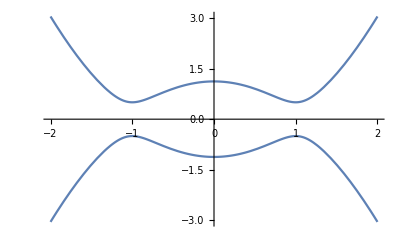

```mathematica
Plot[
ene//.{
ϵk->t*k^2-μ,
μ->1,
t->1,
Δ1->0.5,
Δ2->0},{k,-2,2}]
```

#### Particle-hole character

```mathematica
ConjugateTranspose[egvec[[1]]].tz.egvec[[1]]
```

-1+((-ϵ+√(Δ1^2+Δ2^2+ϵ^2)) (-Conjugate[ϵ]+Conjugate[√(Δ1^2+Δ2^2+ϵ^2)]))/((Δ1+ⅈ Δ2) (Conjugate[Δ1]-ⅈ Conjugate[Δ2]))

```mathematica
ConjugateTranspose[egvec[[2]]].tz.egvec[[2]]
```

-1+((-ϵ-√(Δ1^2+Δ2^2+ϵ^2)) (-Conjugate[ϵ]-Conjugate[√(Δ1^2+Δ2^2+ϵ^2)]))/((Δ1+ⅈ Δ2) (Conjugate[Δ1]-ⅈ Conjugate[Δ2]))

## Gork’kov Equations

```mathematica
h0 = ϵk*IdentityMatrix[2];
h0//MatrixForm

hω=ℏ*ω*IdentityMatrix[2];
hω//MatrixForm

Delta = Δ*PauliMatrix[2];
Delta//MatrixForm
```

(ϵk | 0
0 | ϵk)

```mathematica
hω=ℏ*ω*IdentityMatrix[2];
hω//MatrixForm
```

(0 | -ⅈ Δ
ⅈ Δ | 0)

```mathematica
G =ℏ*Inverse[ (hω-h0-Delta.Inverse[(hω+h0)].ConjugateTranspose[Delta])]//FullSimplify;
G//MatrixForm
```

(-ℏ/(ϵk-ω ℏ+(Δ Conjugate[Δ])/(ϵk+ω ℏ)) | 0
0 | -ℏ/(ϵk-ω ℏ+(Δ Conjugate[Δ])/(ϵk+ω ℏ)))

```mathematica
F=Inverse[(hω+h0)].ConjugateTranspose[Delta].G//MatrixForm//FullSimplify
```

(0 | (ⅈ ℏ Conjugate[Δ])/(ϵk^2-ω^2 ℏ^2+Abs[Δ]^2)
-(ⅈ ℏ Conjugate[Δ])/(ϵk^2-ω^2 ℏ^2+Abs[Δ]^2) | 0)